# Scattering Kernels in 3D

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2022 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

## Draine

Draine, B.T. (2003) ‘Scattering by interstellar dust grains. 1: Optical and ultraviolet’, ApJ., 598, 1017–25.

```mathematica
pDraine[u_,g_,α_]:=1/(4Pi)((1-g^2)/((1+g^2-2 g u)^(3/2))(1+α u^2)/(1+α(1+2 g^2)/3))
```

### Normalization condition

```mathematica
Integrate[2 Pi pDraine[u,g,a],{u,-1,1},Assumptions->0<a<1&&-1<g<1]
```

1

### Mean-cosine

```mathematica
Integrate[2 Pi pDraine[u,g,a]u,{u,-1,1},Assumptions->0<a<1&&-1<g<1]
```

3/5 (g+(2 (1+a) g)/(3+a+2 a g^2))

```mathematica
3/5 (g+(2 (1+a) g)/(3+a+2 a g^2))/.a->0
```

g

### Legendre expansion coefficients

```mathematica
Integrate[2 Pi (2k+1)pDraine[Cos[y],g,a]LegendreP[k,Cos[y]]Sin[y]/.k->0,{y,0,Pi},Assumptions->0<a<1&&-1<g<1]
```

1

```mathematica
Integrate[2 Pi (2k+1)pDraine[Cos[y],g,a]LegendreP[k,Cos[y]]Sin[y]/.k->1,{y,0,Pi},Assumptions->0<a<1&&-1<g<1]
```

(9 g (5+a (3+2 g^2)))/(5 (3+a+2 a g^2))

```mathematica
Integrate[2 Pi (2k+1)pDraine[Cos[y],g,a]LegendreP[k,Cos[y]]Sin[y]/.k->2,{y,0,Pi},Assumptions->0<a<1&&-1<g<1]
```

(14 a+5 (21+11 a) g^2+36 a g^4)/(7 (3+a+2 a g^2))

```mathematica
Integrate[2 Pi (2k+1)pDraine[Cos[y],g,a]LegendreP[k,Cos[y]]Sin[y]/.k->3,{y,0,Pi},Assumptions->0<a<1&&-1<g<1]
```

(g (54 a+7 (45+23 a) g^2+100 a g^4))/(15 (3+a+2 a g^2))

### sampling

```mathematica
cdf=Integrate[2 Pi pDraine[u,g,a],{u,-1,x},Assumptions->0<a<1&&-1<g<1&&-1<x<1]
```

(3 (-1+g) g^2 (-1-g+√(1+g^2-2 g x))+a (2-2 g^6-2 g x-2 √(1+g^2-2 g x)+g^3 √(1+g^2-2 g x)+g^4 (-2+x^2)+2 g^5 (x+√(1+g^2-2 g x))-g^2 (-2+x^2+√(1+g^2-2 g x))))/(2 g^3 (3+a+2 a g^2) √(1+g^2-2 g x))

#### general case

```mathematica
sampleDraineSimplified[xi_,g_,a_]:=Module[{T1,T2,T3,T4,T4a,T5,T6},
T1=(-1+g^2) (4 g^2+a (1+g^2)^2);
T2=-1296 (a-a g^2) (-a+a g^4) T1;
T3=3 g^2 (1+g (-1+2 xi))+a (2+g^2+g^3 (1+2 g^2) (-1+2 xi));
T4a=432 (-a+a g^4)^3+T2+432 (a-a g^2) T3^2;
T4=T4a+√(-4 (-144 a g^2+288 a g^4-144 a g^6)^3+(T4a)^2);
T6=1/(a-a g^2)(2 (-a+a g^4)+(48 2^(1/3) (-a g^2+2 a g^4-a g^6))/T4^(1/3)+T4^(1/3)/(3 2^(1/3)));
T5=6 (1+g^2)+T6;
(1+g^2-(1/2 √(6 (1+g^2)-T6-(8 T3)/(a (-1+g^2) √T5))-(√T5)/2)^2)/(2 g)
]
```

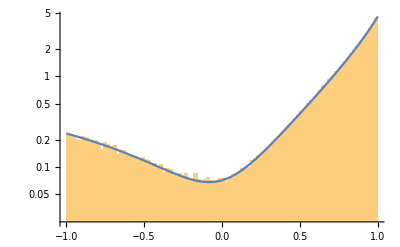

```mathematica
With[{a=6.7,g=.46},Show[Histogram[Table[sampleDraineSimplified[RandomReal[],g,a],{i,1,100000}],100,"PDF",ScalingFunctions->"Log"],
LogPlot[2 Pi pDraine[u,g,a],{u,-1,1},PlotRange->All]
]
]
```

#### special case g = 1/2, a = 12 (useful for approximating Mie scattering of water spheres in air)

```mathematica
pDraine[μ,1/2,12]//FullSimplify
```

(3 (1+12 μ^2))/(14 π (5-4 μ)^(3/2))

Simplification of an exact CDF inverse:

```mathematica
sampleDraineFog[xi_]:=Module[{T1,T2,T3},
T1=√((67+14 xi)^4 (5239-102376 xi+492072 xi^2+105056 xi^3+5488 xi^4));
T2=(883297-8820952 xi+2597784 xi^2+735392 xi^3+38416 xi^4+√7 T1)^(1/3);
T3=√((3954 2^(2/3) 3^(1/3)-56280 2^(2/3) 3^(1/3) xi-5880 2^(2/3) 3^(1/3) xi^2+912 T2+2^(1/3) 3^(2/3) T2^2)/T2);
1/12 (-30-T3+√(1824+(6 2^(2/3) 3^(1/3) (-659+9380 xi+980 xi^2))/T2-2^(1/3) 3^(2/3) T2+(12 (67+14 xi)^2)/(T3)))
]
```

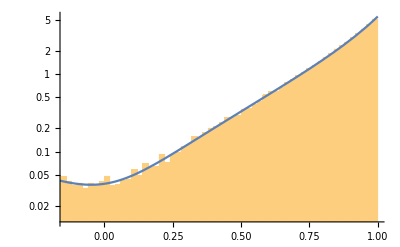

```mathematica
Show[Histogram[Table[sampleDraineFog[RandomReal[]],{i,1,100000}],100,"PDF",ScalingFunctions->"Log"],
LogPlot[2 Pi pDraine[u,.5,12.],{u,-1,1},PlotRange->All]

]
```